## Naloga 1

Sestavite funkcijo igra[l_], kot je zapisano v navodilih.

```mathematica
poteza[l_]:=With[{pos=First[First[Position[l,First[Select[l,#<0&]]]]]},
l+Table[If[i==pos,-2*l[[pos]],If[MemberQ[{1,4},Abs[pos-i]],l[[pos]],0]],{i,1,5}]
]
igra[l_]/;Min[l]≥0:={l}
igra[l_]:=Prepend[igra[poteza[l]],l]
```

```mathematica
igra[{1,4,-1,-3,2}]
```

{{1,4,-1,-3,2},{1,3,1,-4,2},{1,3,-3,4,-2},{1,0,3,1,-2},{-1,0,3,-1,2},{1,-1,3,-1,1},{0,1,2,-1,1},{0,1,1,1,0}}

Sestavite funkcijo igra2[l_], kot je zapisano v navodilih.

```mathematica
poteza2[l_]:=With[{pos=First[RandomChoice[Position[l,Min[l]]]]},
l+Table[If[i==pos,-2*l[[pos]],If[MemberQ[{1,4},Abs[pos-i]],l[[pos]],0]],{i,1,5}]
]
igra2[l_]/;Min[l]≥0:={l}
igra2[l_]:=Prepend[igra2[poteza2[l]],l]
```

```mathematica
igra2[{1,4,-1,-3,2}]
```

{{1,4,-1,-3,2},{1,4,-4,3,-1},{1,0,4,-1,-1},{1,0,3,1,-2},{-1,0,3,-1,2},{-1,0,2,1,1},{1,-1,2,1,0},{0,1,1,1,0}}

```mathematica
igra2[{1,4,-1,-3,2}]
```

{{1,4,-1,-3,2},{1,4,-4,3,-1},{1,0,4,-1,-1},{0,0,4,-2,1},{0,0,2,2,-1},{-1,0,2,1,1},{1,-1,2,1,0},{0,1,1,1,0}}

## Naloga 2

Sestavite funkcijo nanocevka[n_], kot je zapisano v navodilih.

```mathematica
PolarToCartesian[{r_,fi_}]:={r*Cos[fi],r*Sin[fi]}
nanoLines[0]:={Table[PolarToCartesian[{2,Pi/2+i*2Pi/6}],{i,0,6}]}
nanoLines[n_Integer]:=Join[
{Table[PolarToCartesian[{(3*n+1)+1*Mod[i+n+1,2],Pi/2+i*2Pi/12}],{i,0,12}]},
Join[Table[{PolarToCartesian[{3*n-1,Mod[n+1,2]*Pi/6+Pi/2+i*2Pi/6}],PolarToCartesian[{3*n+1,Mod[n+1,2]*Pi/6+Pi/2+i*2Pi/6}]},{i,0,5}]],
nanoLines[n-1]
]
nanocevka[n_Integer]:=Graphics[Line[nanoLines[n]]]
```

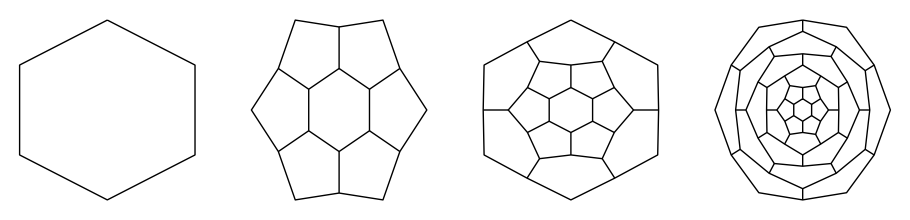

```mathematica
GraphicsRow[{nanocevka[0],nanocevka[1],nanocevka[2],nanocevka[5]}]
```